```mathematica
img=ImageRotate[ColorConvert[-Graphics-,"Grayscale"],0]
dat=ImageData[img][[;;,;;,1]];
dat/=Max[dat];
```

-Graphics-

```mathematica
Dimensions[dat]
```

{}

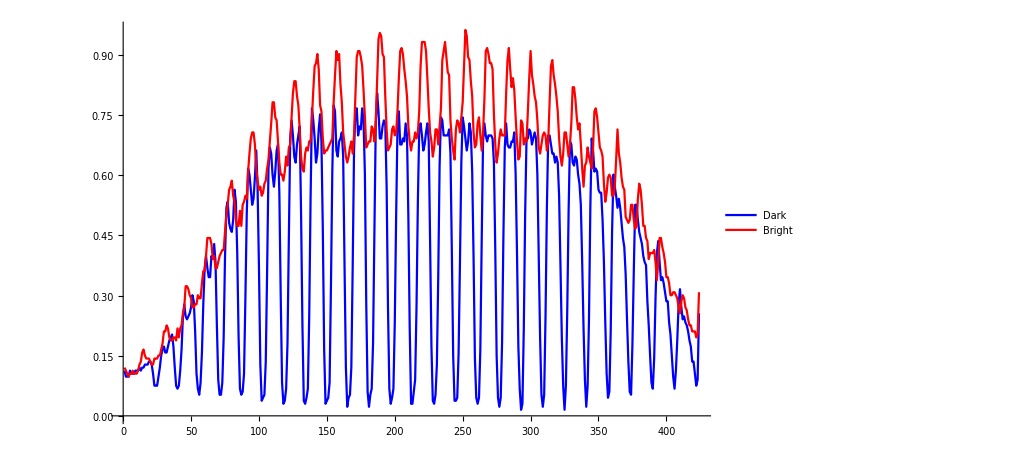

```mathematica
ListPlot[{dat[[149]],dat[[157]]},Joined->True,PlotStyle->{Blue,Red},PlotLegends->{"Dark","Bright"}]
```

```mathematica
pixels=Range[Length[dat[[;;,0]]]];
ListPlot[{Transpose@{dat[[149]],pixels},Transpose@dat[[157]]},Joined->True]
```

Transpose::nmtx: The first two levels of {{{0.0588235,1.},{0.0509804,1.},{0.0509804,1.},{0.0509804,1.},{0.0588235,1.},{0.054902,1.},{0.054902,1.},{0.054902,1.},{0.0588235,1.},{0.0588235,1.},«414»},{1,2,3,4,5,6,7,8,9,10,«334»}} cannot be transposed.

Transpose::nmtx: The first two levels of {{{0.0588235,1.},{0.0509804,1.},{0.0509804,1.},{0.0509804,1.},{0.0588235,1.},{0.054902,1.},{0.054902,1.},{0.054902,1.},{0.0588235,1.},{0.0588235,1.},«414»},{1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,«334»}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

-Graphics-

```mathematica
dat[[149]]
```

{{0.0588235,1.},{0.0509804,1.},{0.0509804,1.},{0.0509804,1.},{0.0588235,1.},{0.054902,1.},{0.054902,1.},{0.054902,1.},{0.0588235,1.},{0.0588235,1.},{0.0588235,1.},{0.0627451,1.},{0.0588235,1.},{0.0627451,1.},{0.0627451,1.},{0.0666667,1.},{0.0666667,1.},{0.0666667,1.},{0.0705882,1.},{0.0705882,1.},{0.0666667,1.},{0.054902,1.},{0.0392157,1.},{0.0392157,1.},{0.0392157,1.},{0.0509804,1.},{0.0627451,1.},{0.0784314,1.},{0.0862745,1.},{0.0901961,1.},{0.0823529,1.},{0.0823529,1.},{0.0901961,1.},{0.0980392,1.},{0.101961,1.},{0.105882,1.},{0.0901961,1.},{0.0627451,1.},{0.0392157,1.},{0.0352941,1.},{0.0392157,1.},{0.0588235,1.},{0.0862745,1.},{0.129412,1.},{0.145098,1.},{0.129412,1.},{0.12549,1.},{0.129412,1.},{0.133333,1.},{0.141176,1.},{0.156863,1.},{0.14902,1.},{0.109804,1.},{0.054902,1.},{0.0352941,1.},{0.027451,1.},{0.0431373,1.},{0.0823529,1.},{0.145098,1.},{0.192157,1.},{0.207843,1.},{0.192157,1.},{0.180392,1.},{0.180392,1.},{0.207843,1.},{0.203922,1.},{0.223529,1.},{0.2,1.},{0.117647,1.},{0.0470588,1.},{0.027451,1.},{0.027451,1.},{0.0431373,1.},{0.101961,1.},{0.207843,1.},{0.270588,1.},{0.278431,1.},{0.25098,1.},{0.243137,1.},{0.239216,1.},{0.254902,1.},{0.294118,1.},{0.278431,1.},{0.211765,1.},{0.101961,1.},{0.0352941,1.},{0.027451,1.},{0.0313725,1.},{0.054902,1.},{0.152941,1.},{0.262745,1.},{0.321569,1.},{0.313725,1.},{0.294118,1.},{0.27451,1.},{0.282353,1.},{0.309804,1.},{0.345098,1.},{0.294118,1.},{0.192157,1.},{0.0666667,1.},{0.0196078,1.},{0.0235294,1.},{0.027451,1.},{0.0705882,1.},{0.188235,1.},{0.321569,1.},{0.34902,1.},{0.341176,1.},{0.313725,1.},{0.298039,1.},{0.317647,1.},{0.345098,1.},{0.352941,1.},{0.290196,1.},{0.156863,1.},{0.0431373,1.},{0.0156863,1.},{0.0196078,1.},{0.0352941,1.},{0.0941176,1.},{0.231373,1.},{0.360784,1.},{0.384314,1.},{0.364706,1.},{0.337255,1.},{0.329412,1.},{0.352941,1.},{0.364706,1.},{0.376471,1.},{0.262745,1.},{0.117647,1.},{0.0196078,1.},{0.0156863,1.},{0.0235294,1.},{0.0352941,1.},{0.129412,1.},{0.282353,1.},{0.4,1.},{0.384314,1.},{0.360784,1.},{0.329412,1.},{0.341176,1.},{0.372549,1.},{0.392157,1.},{0.356863,1.},{0.243137,1.},{0.0862745,1.},{0.0156863,1.},{0.0196078,1.},{0.0235294,1.},{0.0431373,1.},{0.168627,1.},{0.317647,1.},{0.403922,1.},{0.396078,1.},{0.345098,1.},{0.337255,1.},{0.356863,1.},{0.360784,1.},{0.368627,1.},{0.337255,1.},{0.196078,1.},{0.0627451,1.},{0.0117647,1.},{0.0235294,1.},{0.027451,1.},{0.0627451,1.},{0.192157,1.},{0.345098,1.},{0.396078,1.},{0.4,1.},{0.364706,1.},{0.376471,1.},{0.372549,1.},{0.4,1.},{0.384314,1.},{0.313725,1.},{0.145098,1.},{0.0313725,1.},{0.0117647,1.},{0.027451,1.},{0.0352941,1.},{0.0941176,1.},{0.239216,1.},{0.380392,1.},{0.419608,1.},{0.396078,1.},{0.360784,1.},{0.360784,1.},{0.376471,1.},{0.384314,1.},{0.380392,1.},{0.298039,1.},{0.141176,1.},{0.0352941,1.},{0.0156863,1.},{0.0235294,1.},{0.0352941,1.},{0.121569,1.},{0.258824,1.},{0.376471,1.},{0.396078,1.},{0.352941,1.},{0.352941,1.},{0.360784,1.},{0.356863,1.},{0.380392,1.},{0.364706,1.},{0.258824,1.},{0.113725,1.},{0.0156863,1.},{0.0156863,1.},{0.0313725,1.},{0.0470588,1.},{0.141176,1.},{0.278431,1.},{0.372549,1.},{0.380392,1.},{0.364706,1.},{0.345098,1.},{0.352941,1.},{0.368627,1.},{0.380392,1.},{0.356863,1.},{0.227451,1.},{0.0901961,1.},{0.0196078,1.},{0.0156863,1.},{0.027451,1.},{0.0666667,1.},{0.180392,1.},{0.32549,1.},{0.388235,1.},{0.384314,1.},{0.364706,1.},{0.364706,1.},{0.364706,1.},{0.364706,1.},{0.372549,1.},{0.341176,1.},{0.215686,1.},{0.0784314,1.},{0.0196078,1.},{0.0196078,1.},{0.0235294,1.},{0.0823529,1.},{0.2,1.},{0.329412,1.},{0.388235,1.},{0.376471,1.},{0.360784,1.},{0.345098,1.},{0.356863,1.},{0.380392,1.},{0.368627,1.},{0.317647,1.},{0.207843,1.},{0.0745098,1.},{0.0235294,1.},{0.0156863,1.},{0.0235294,1.},{0.0862745,1.},{0.227451,1.},{0.356863,1.},{0.380392,1.},{0.364706,1.},{0.356863,1.},{0.364706,1.},{0.364706,1.},{0.364706,1.},{0.360784,1.},{0.329412,1.},{0.215686,1.},{0.0784314,1.},{0.0235294,1.},{0.0117647,1.},{0.0235294,1.},{0.0941176,1.},{0.235294,1.},{0.34902,1.},{0.380392,1.},{0.352941,1.},{0.34902,1.},{0.34902,1.},{0.356863,1.},{0.356863,1.},{0.368627,1.},{0.313725,1.},{0.211765,1.},{0.0901961,1.},{0.0352941,1.},{0.00784314,1.},{0.0156863,1.},{0.113725,1.},{0.262745,1.},{0.360784,1.},{0.360784,1.},{0.372549,1.},{0.368627,1.},{0.352941,1.},{0.360784,1.},{0.368627,1.},{0.360784,1.},{0.313725,1.},{0.207843,1.},{0.101961,1.},{0.027451,1.},{0.0117647,1.},{0.027451,1.},{0.129412,1.},{0.270588,1.},{0.364706,1.},{0.364706,1.},{0.352941,1.},{0.341176,1.},{0.341176,1.},{0.329412,1.},{0.337255,1.},{0.329412,1.},{0.286275,1.},{0.196078,1.},{0.101961,1.},{0.0392157,1.},{0.00784314,1.},{0.0392157,1.},{0.137255,1.},{0.266667,1.},{0.356863,1.},{0.352941,1.},{0.329412,1.},{0.32549,1.},{0.337255,1.},{0.333333,1.},{0.313725,1.},{0.301961,1.},{0.27451,1.},{0.2,1.},{0.113725,1.},{0.0470588,1.},{0.0117647,1.},{0.0392157,1.},{0.12549,1.},{0.270588,1.},{0.360784,1.},{0.345098,1.},{0.317647,1.},{0.321569,1.},{0.317647,1.},{0.294118,1.},{0.290196,1.},{0.290196,1.},{0.254902,1.},{0.2,1.},{0.121569,1.},{0.054902,1.},{0.0235294,1.},{0.0313725,1.},{0.109804,1.},{0.239216,1.},{0.313725,1.},{0.298039,1.},{0.286275,1.},{0.270588,1.},{0.282353,1.},{0.270588,1.},{0.25098,1.},{0.231373,1.},{0.219608,1.},{0.184314,1.},{0.12549,1.},{0.0705882,1.},{0.0313725,1.},{0.027451,1.},{0.0941176,1.},{0.188235,1.},{0.27451,1.},{0.27451,1.},{0.254902,1.},{0.239216,1.},{0.231373,1.},{0.223529,1.},{0.207843,1.},{0.2,1.},{0.196078,1.},{0.14902,1.},{0.117647,1.},{0.0784314,1.},{0.0431373,1.},{0.0352941,1.},{0.0745098,1.},{0.152941,1.},{0.211765,1.},{0.227451,1.},{0.2,1.},{0.176471,1.},{0.180392,1.},{0.172549,1.},{0.160784,1.},{0.14902,1.},{0.14902,1.},{0.121569,1.},{0.105882,1.},{0.0784314,1.},{0.0509804,1.},{0.0352941,1.},{0.0588235,1.},{0.0980392,1.},{0.145098,1.},{0.164706,1.},{0.141176,1.},{0.12549,1.},{0.129412,1.},{0.121569,1.},{0.117647,1.},{0.109804,1.},{0.0980392,1.},{0.0901961,1.},{0.0705882,1.},{0.0705882,1.},{0.054902,1.},{0.0392157,1.},{0.0470588,1.},{0.133333,1.}}

-Graphics-

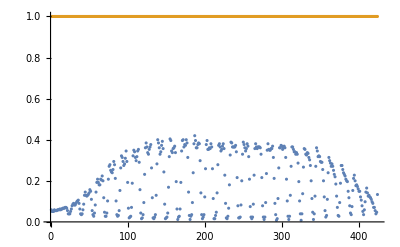

```mathematica
ListPlot[Transpose@dat[[149]]]
```

```mathematica
ListPlot[]
```

Part::partd: Part specification … is longer than depth of object.

Part::pkspec1: The expression False cannot be used as a part specification.

ListPlot::lpn: … is not a list of numbers or pairs of numbers.

ListPlot[(-Graphics-)⟦149,1;;All⟧]

```mathematica
img[[149,149]]
```

Part::partd: Part specification … is longer than depth of object.

(-Graphics-)⟦149,149⟧